```mathematica
(*The first point is from 1007.2580*)
a={0.2824,0.2556,0.2490,0.2425,0.2361,0.2297,0.2235,0.2173,0.2142,0.2112,0.2052,0.1994,0.1937,0.1908,0.1881,0.1826,0.1773,0.1722,0.1672,0.1625,0.1579,0.1535,0.1493,0.1453,0.1416,0.1379,0.1345,0.1312,0.1280,0.1249,0.1110};
beta={3.45,3.490,3.500,3.510,3.520,3.530,3.540,3.550,3.555,3.560,3.570,3.580,3.590,3.595,3.600,3.610,3.620,3.630,3.640,3.650,3.660,3.670,3.680,3.690,3.700,3.710,3.720,3.730,3.740,3.750,3.800};
ms={0.157,0.132,0.126,0.121,0.116,0.111,0.10643,0.10200,0.09987,0.09779,0.09378,0.08998,0.08638,0.08465,0.08296,0.07973,0.07668,0.07381,0.07110,0.06854,0.06615,0.06390,0.06179,0.05982,0.05797,0.05624,0.05462,0.05309,0.05166,0.05030,0.04445};
```

```mathematica
betaa=Interpolation[Transpose[{a,beta}]];
msa=Interpolation[Transpose[{a,ms}]];
```

```mathematica
aval=0.207349643812;
betaa[aval]
msa[aval]
```

3.5664

0.0952001

```mathematica
abeta = Interpolation[Transpose[{beta, a}]];
betaval = 3.45887;
abeta[betaval]
```

0.276459

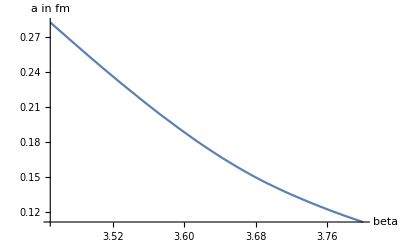

```mathematica
Plot[abeta[beta], {beta, 3.45, 3.8 }, AxesLabel->{HoldForm[beta],HoldForm[a in fm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
T[x_] := (1/(abeta[x] 6))/5.068
```

SetDelayed::write: Tag Real in 0.118955[x_] is Protected.

```mathematica
T[3.45]
```

0.118955[3.45]

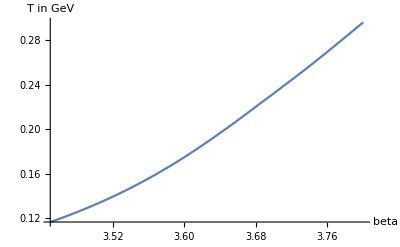

```mathematica
Plot[(1/(abeta[beta] 6))/5.068, {beta, 3.45, 3.8 }, AxesLabel->{HoldForm[beta],HoldForm[T in GeV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
B[n_] := (2 π 3/2 n)/(24^2 abeta[betaval]^2)
```

```mathematica
B[6]
```

1.28452